```mathematica
input= //StringTrim ;
```

```mathematica
inputSplit =  StringSplit[input ,","];
```

```mathematica
inputSplit // Length
```

4000

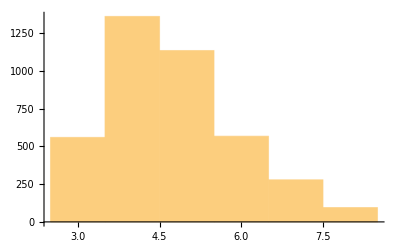

```mathematica
StringLength /@ inputSplit // Histogram
```

We can see, the problem is, the length of each “steps” is not the same, so we must use some kind of recursion function.

```mathematica
Fold[f,x,{a,b,c,d}]
```

f[f[f[f[x,a],b],c],d]

```mathematica
convertStepToValue[currentValue_Integer,char_String]:= Module[{
ascii = ToCharacterCode[char][[1]]
},
QuotientRemainder[((currentValue + ascii)* 17 ),256][[2]]
];
```

```mathematica
Fold[convertStepToValue,0,StringSplit["HASH",""]]
```

52

Good!

```mathematica
Fold[convertStepToValue,0,StringSplit[#,""]]& /@ inputSplit  //Total
```

513172

Actually we can finish part 1 in just 1 line .

(ノ＞▽＜。) ノ, this problem seem easy. I just got lucky after skip the second week did not solve anything!

## Part 2

Hilarious, part 2 description is the most confusing thing I have to read . The problem of AOC is that, the statements given is so lengthy and wordy, normally we just skim thought a few sentences that related to the example.  But today the example lack of the explanation steps by steps.

-Graphics-

How we know what box each “step” we need to put in. There is no explanation. Until I read try to go back and read this sentences -Graphics-

Oh, it clears, we must understand here “label” mean only “rn” in “rn=1”. After pipe the “rn” to part 1 hash algorithm we will receive 0 as output. Similar to other step. That explain why there is exactly 256 boxes, because the remaining  <= divisor.

Now, everything seem easy . Strategy is here. 

We find the box number each step belong to. Simply just using the algorithm in part 1. 

We treat each box as a main element. Apply  all the step related to each box using folding as above. 

You can see the beautiful of Wolfram language than python, it using most of functional style  - recursive folding but still apply a same result like for loop in other imperative language. Mathematic is truly language of natural, it can model anything.

```mathematica
parseStep[step_String]:= Module[{},
 Piecewise[{{<|"step"-> step,
"operator"->"-",
"box" -> Fold[convertStepToValue,0,StringSplit[#,""]]& @StringTake[step,{1,-2}],

"label"->StringTake[step,{1,-2}] |>, StringSplit[step,""][[-1]] == "-"}, {<|"step"-> step,
"operator"->"=",
"box" -> Fold[convertStepToValue,0,StringSplit[#,""]]& @StringSplit[step,"="][[1]],
"focusLength"->( StringSplit[step,"="][[2]]//ToExpression),
"label"-> StringSplit[step,"="][[1]]
 |>, (StringSplit[step,"="] // Length) ==2}, {-1, True}}]
]
```

```mathematica
{parseStep["dxd=1"], parseStep["yes-"]}
```

{<|step→dxd=1,operator→=,box→64,focusLength→1,label→dxd|>,<|step→yes-,operator→-,box→209,label→yes|>}

```mathematica
steps = parseStep /@ inputSplit ;
```

```mathematica
steps //Select[#,-1]&
```

{}

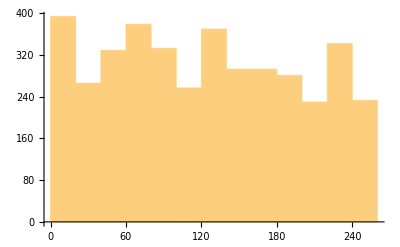

```mathematica
#["box"]& /@ steps //Histogram
```

Nice, now we group those steps base on box

```mathematica
boxs = GroupBy[steps,#["box"]&] //KeySort;
```

```mathematica
boxs
```

```mathematica
box0Ds =boxs[0] //Dataset
```

```mathematica
box0Ds[All,"label",# == "vjzjnn"&] // Select[#,TrueQ]& //Length
```

12

```mathematica
#["label"]& /@ steps // Select[#,#=="vjzjnn"&]& //Length
```

12

Okie, I just want to check if data is corrupted or not

Now, the problems is, how to model the solution, never using those imperative loop in wolfram or lisp language

```mathematica
boxs[0]
```

{<|step→vjzjnn-,operator→-,box→0,label→vjzjnn|>,<|step→vjzjnn=8,operator→=,box→0,focusLength→8,label→vjzjnn|>,<|step→vrtgm=7,operator→=,box→0,focusLength→7,label→vrtgm|>,<|step→vjzjnn-,operator→-,box→0,label→vjzjnn|>,<|step→vrtgm-,operator→-,box→0,label→vrtgm|>,<|step→vrtgm-,operator→-,box→0,label→vrtgm|>,<|step→vjzjnn=8,operator→=,box→0,focusLength→8,label→vjzjnn|>,<|step→vjzjnn=8,operator→=,box→0,focusLength→8,label→vjzjnn|>,<|step→vjzjnn-,operator→-,box→0,label→vjzjnn|>,<|step→vjzjnn-,operator→-,box→0,label→vjzjnn|>,<|step→vjzjnn-,operator→-,box→0,label→vjzjnn|>,<|step→vrtgm-,operator→-,box→0,label→vrtgm|>,<|step→vjzjnn=2,operator→=,box→0,focusLength→2,label→vjzjnn|>,<|step→vrtgm=7,operator→=,box→0,focusLength→7,label→vrtgm|>,<|step→vjzjnn=1,operator→=,box→0,focusLength→1,label→vjzjnn|>,<|step→vrtgm-,operator→-,box→0,label→vrtgm|>,<|step→vrtgm=6,operator→=,box→0,focusLength→6,label→vrtgm|>,<|step→vjzjnn-,operator→-,box→0,label→vjzjnn|>,<|step→vjzjnn-,operator→-,box→0,label→vjzjnn|>}

```mathematica
boxs //Length
```

239

```mathematica
addLensToBoxByStep[box_List,step_Association]:=Module[{},
Piecewise[{{Piecewise[{{box /. s_/;s["label"]== step["label"] -> step, (Select[box,#["label"]== step["label"]&]//Length )==1}, {Append[box,step], (Select[box,#["label"]== step["label"]&]//Length )== 0}}], step["operator"]=="="}, {DeleteCases[box,s_/;s["label"] == step["label"]], step["operator"]=="-"}}]
]
```

```mathematica
addLensToBoxByStep[{},<|"step"->"rn=1","operator"->"=","box"->0,"focusLength"->1,"label"->"rn"|>]
```

{<|step→rn=1,operator→=,box→0,focusLength→1,label→rn|>}

```mathematica
Fold[addLensToBoxByStep,{},boxs[3]]
```

{<|step→vlq=8,operator→=,box→3,focusLength→8,label→vlq|>}

```mathematica
boxesAfterPutLens = Fold[addLensToBoxByStep,{},#]& /@ boxs;
```

```mathematica
boxesAfterPutLens //Shallow
```

<|0→{<|step→vrtgm=6,operator→=,box→0,focusLength→6,label→vrtgm|>},1→{<|step→qp=9,operator→=,box→1,focusLength→9,label→qp|>},2→{<|step→jfr=1,operator→=,box→2,focusLength→1,label→jfr|>},3→{<|step→vlq=8,operator→=,box→3,focusLength→8,label→vlq|>},4→{<|step→jtf=7,operator→=,box→4,focusLength→7,label→jtf|>},5→{<|step→rrq=9,operator→=,box→5,focusLength→9,label→rrq|>,<|step→fsbtv=3,operator→=,box→5,focusLength→3,label→fsbtv|>},7→{<|step→qsc=5,operator→=,box→7,focusLength→5,label→qsc|>,<|step→lk=5,operator→=,box→7,focusLength→5,label→lk|>},8→{<|step→km=6,operator→=,box→8,focusLength→6,label→km|>},9→{<|step→tkj=3,operator→=,box→9,focusLength→3,label→tkj|>},10→{<|step→xr=8,operator→=,box→10,focusLength→8,label→xr|>,<|step→nvf=2,operator→=,box→10,focusLength→2,label→nvf|>},«229»|>

```mathematica
Length /@boxesAfterPutLens
```

<|0→1,1→1,2→1,3→1,4→1,5→2,7→2,8→1,9→1,10→2,11→4,12→1,13→0,14→0,15→0,16→1,17→1,18→1,19→4,20→1,21→1,22→1,23→3,24→3,25→2,27→0,28→1,29→0,30→1,32→2,33→1,34→0,35→2,36→1,37→2,38→1,39→1,40→0,41→0,42→0,43→1,44→2,45→1,46→0,47→0,48→1,49→1,50→1,51→1,52→0,53→0,54→0,55→0,56→0,57→2,59→2,60→1,61→1,62→2,63→2,64→2,65→2,66→1,67→0,68→0,69→2,70→0,71→2,72→3,73→2,74→0,75→3,76→0,77→1,78→1,79→2,80→1,81→2,82→1,83→0,84→1,85→2,86→2,87→1,88→2,89→2,90→0,91→1,92→2,93→2,94→2,95→1,96→0,97→0,98→2,99→0,100→1,101→0,102→2,104→1,106→1,107→1,108→0,109→1,110→1,111→2,112→0,113→1,114→1,115→1,117→2,118→1,119→1,120→0,121→0,122→2,123→1,124→0,125→1,126→1,127→0,128→2,129→1,130→3,131→2,132→0,133→0,134→2,135→4,136→1,137→1,138→0,140→0,142→0,143→1,144→3,145→1,146→2,147→1,148→3,149→1,150→4,151→1,152→1,153→0,154→1,155→1,156→0,157→1,158→1,159→2,160→0,161→0,162→2,163→2,164→1,165→0,166→0,168→2,169→1,170→1,171→1,172→3,174→0,175→0,176→2,177→1,178→0,179→1,180→3,181→1,182→0,183→3,184→2,185→1,186→2,187→0,188→3,189→1,190→1,191→1,193→0,194→1,195→2,197→1,198→0,199→2,200→0,201→1,202→2,203→0,204→1,205→0,206→0,207→1,208→1,210→2,211→1,212→1,213→0,214→0,215→1,216→2,218→2,219→0,220→1,221→1,222→1,224→1,225→0,226→1,227→1,228→0,229→1,230→0,231→0,232→2,233→2,234→0,235→1,236→1,237→2,238→3,239→3,240→0,242→1,243→0,244→0,245→2,246→0,247→0,248→2,249→1,250→2,251→3,252→1,253→1,254→0,255→0|>

Good, we have 256 boxes , some box don’t have any  lens suitable and some box have multi lens;

Now thing seem easy, a function to calculate the power of each box contain

-Graphics-

```mathematica
valueOfBox[box_List] := Module[{
lenPositions = PositionIndex[box]
},
(#["box"] + 1)* lenPositions[#][[1]]  * #["focusLength"] & /@ box //Total

]
```

```mathematica
valueOfBox[boxesAfterPutLens[[1]]]
```

6

Good!

```mathematica
valueOfBox /@ boxesAfterPutLens //Total
```

237806

## Scratchpad

```mathematica
PositionIndex[{a,b,c,a,a}]
```

<|a→{1,4,5},b→{2},c→{3}|>

```mathematica
StringTake["abc",{1,-2}]
```

ab

```mathematica
SetDirectory["~/nhannht-projects/aoc2023"];
```

```mathematica
NotebookSave[EvaluationNotebook[],FileNameJoin[{Directory[],"15.nb"}]]
```

```mathematica
( Fold[convertStepToValue,0,StringSplit[#,""]]& /@ inputSplit ) //Max
```

255

```mathematica
Fold[convertStepToValue,0,StringSplit["rn",""]]
```

0

```mathematica
SetOptions[SelectedNotebook[],PrintingStyleEnvironment->"Printout",ShowSyntaxStyles->True]
```

```mathematica
Export["15.pdf",EvaluationNotebook[]]
```

15.pdf

```mathematica
SystemOpen["15.pdf"]
```

```mathematica
SystemOpen["15.pdf"]
```